This Mathematica notebook reproduces the figures include in the Handbook of Social Economics chapter "Econometric methods for the analysis of assignment problems in the presence of complementarity and social spillovers" by Bryan Graham.

```mathematica
<<ComputationalGeometry`
<<Graphics`FilledPlot`
```

General::obspkg: Graphics`FilledPlot` is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

```mathematica
mH[s_,αH_,βH_,γH_]:=αH+βH*s-γH/2*s^2;
mL[s_,αL_,βL_,γL_]:=αL+βL*s-γL/2*s^2;
m[s_,αL_,βL_,γL_,αH_,βH_,γH_]:=s*mH[s,αH,βH,γH]+(1-s)*mL[s,αL,βL,γL];
MMB[s_,βL_,γL_,βH_,γH_]:=(βH-βL)-(γH-γL)*s;
MSB[s_,βL_,γL_,βH_,γH_]:=(βH-βL)-(γH-γL)*s-(s*γH+(1-s)*γL);
```

### Example 1: Efficient segregation

```mathematica
αH=0.05;
βH=1;
γH=1/4;
```

```mathematica
αL=0;
βL=1/2;
γL=1/4;
```

```mathematica
pH=0.5
```

0.5

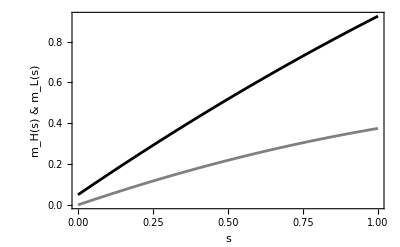

```mathematica
mHmLPlotEx1=Plot[{mH[s,αH,βH,γH],mL[s,αL,βL,γL]},{s,0,1},PlotStyle->{{GrayLevel[0],Thickness[0.005]},{GrayLevel[0.5],Thickness[0.005]}},Frame->True,FrameLabel->{StyleForm["s",FontSize->12],StyleForm["m_H(s)  &  m_L(s)",FontSize->12],StyleForm["Panel A.1",FontSize->12],""}]
```

```mathematica
mlist=Table[{s,m[s,αL,βL,γL,αH,βH,γH]},{s,0,1,0.01}];
t=Table[{s,m[0,αL,βL,γL,αH,βH,γH]},{s,0,1,0.01}];
u=Table[{1,m[0,αL,βL,γL,αH,βH,γH]+(m[s,αL,βL,γL,αH,βH,γH]-m[0,αL,βL,γL,αH,βH,γH])*s},{s,0,1,0.01}];
v=Drop[Sort[ConvexHull[Join[mlist,t,u]]],-199];
ConvHullm=mlist[[v]];
```

ConvexHull::duplicated: 3 duplicated point(s) ignored.

```mathematica
sL=mlist[[v[[1]]]]
sR=mlist[[v[[2]]]]
```

{0.,0.}

{1.,0.925}

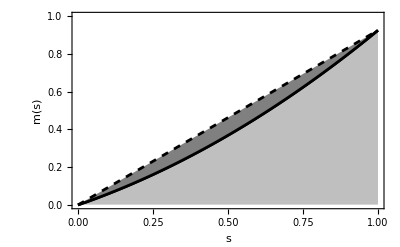

```mathematica
FilledListPlot[mlist,ConvHullm,t,Frame->True,FrameLabel->{StyleForm["s",FontSize->12],StyleForm["m(s)",FontSize->12],StyleForm["Panel C.1",FontSize->12],""},PlotJoined -> {True,True},PlotRange->{{0,1},{0,1}},SymbolShape->{None,None},PlotStyle->{{GrayLevel[0],Thickness[0.005]},{Dashing[{0.0125,0.0125}],GrayLevel[0],Thickness[0.005]},{GrayLevel[1],Thickness[0.001]}},Fills->{{{1,3},GrayLevel[0.75]},{{1,2},GrayLevel[0.5]}}]
```

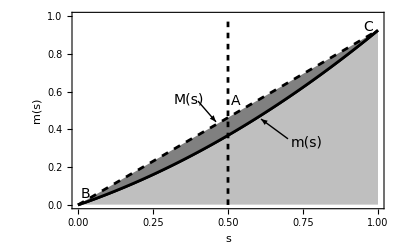

```mathematica
SocPlanPlotEx1=Show[%,Graphics[{{Thickness[0.005],GrayLevel[0],Dashing[{0.01,0.01}],Line[{{pH,0},{pH,1}}]},
		Text[StyleForm["A",FontSize->14],{pH+0.01,0.55},{-1,0}],Text[StyleForm["B",FontSize->14],sL+{0.01,0.06},{-1,0}],Text[StyleForm["C",FontSize->14],sR-{0.015,-0.015},{1,0}],Arrow[{{0.40,0.55},{0.46,0.44}}],	Text[StyleForm["M(s)",FontSize->14],{0.32,0.56},{-1,0}],Arrow[{{0.70,0.35},{0.61,0.455}}],	Text[StyleForm["m(s)",FontSize->14],{0.71,0.33},{-1,0}]}]]
```

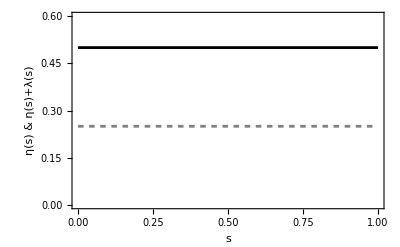

```mathematica
MSPlotEx1=Plot[{MMB[s,βL,γL,βH,γH],MSB[s,βL,γL,βH,γH]},{s,0,1},PlotStyle->{{GrayLevel[0],Thickness[0.005]},{GrayLevel[0.5],Thickness[0.005],Dashing[{0.01,0.01}]},{GrayLevel[0],Thickness[0.005],Dashing[{0.01,0.01}]}},Frame->True,FrameLabel->{StyleForm["s",FontSize->12],StyleForm["η(s) & η(s)+λ(s)",FontSize->12],StyleForm["Panel B.1",FontSize->12],""},PlotRange->{{0,1},{0,0.6}}]
```

### Example 2: Inefficient segregation

```mathematica
αH=0.05;
βH=3/4;
γH=2/3;
```

```mathematica
αL=0;
βL=2/3;
γL=2/3;
```

```mathematica
pH=0.5
```

0.5

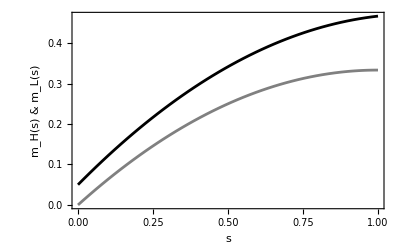

```mathematica
mHmLPlotEx2=Plot[{mH[s,αH,βH,γH],mL[s,αL,βL,γL]},{s,0,1},PlotStyle->{{GrayLevel[0],Thickness[0.005]},{GrayLevel[0.5],Thickness[0.005]}},Frame->True,FrameLabel->{StyleForm["s",FontSize->12],StyleForm["m_H(s)  &  m_L(s)",FontSize->12],StyleForm["Panel A.2",FontSize->12],""}]
```

```mathematica
mlist=Table[{s,m[s,αL,βL,γL,αH,βH,γH]},{s,0,1,0.01}];
t=Table[{s,m[0,αL,βL,γL,αH,βH,γH]},{s,0,1,0.01}];
u=Table[{1,m[0,αL,βL,γL,αH,βH,γH]+(m[s,αL,βL,γL,αH,βH,γH]-m[0,αL,βL,γL,αH,βH,γH])*s},{s,0,1,0.01}];
v=Drop[Sort[ConvexHull[Join[mlist,t,u]]],-199];
ConvHullm=mlist[[v]];
```

ConvexHull::duplicated: 3 duplicated point(s) ignored.

```mathematica
sL=mlist[[v[[1]]]]
sR=mlist[[v[[2]]]]
```

{0.,0.}

{0.01,0.00714167}

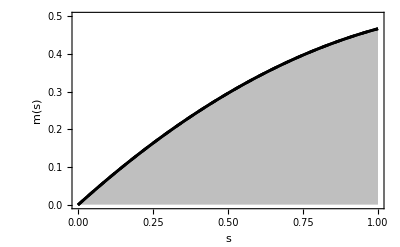

```mathematica
FilledListPlot[mlist,ConvHullm,t,Frame->True,FrameLabel->{StyleForm["s",FontSize->12],StyleForm["m(s)",FontSize->12],StyleForm["Panel C.2",FontSize->12],""},PlotJoined -> {True,True},PlotRange->{{0,1},{0,0.5}},SymbolShape->{None,None},PlotStyle->{{GrayLevel[0],Thickness[0.005]},{Dashing[{0.0125,0.0125}],GrayLevel[0],Thickness[0.005]},{GrayLevel[1],Thickness[0.001]}},Fills->{{{1,3},GrayLevel[0.75]},{{1,2},GrayLevel[0.5]}}]
```

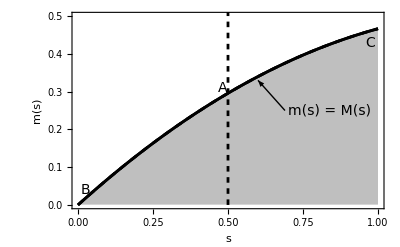

```mathematica
SocPlanPlotEx2=Show[%,Graphics[{{Thickness[0.005],GrayLevel[0],Dashing[{0.01,0.01}],Line[{{pH,0},{pH,1}}]},
		Text[StyleForm["A",FontSize->14],{pH-0.035,0.31},{-1,0}],Text[StyleForm["B",FontSize->14],{0.01,0.04},{-1,0}],Text[StyleForm["C",FontSize->14],{0.99,0.43},{1,0}],Arrow[{{0.69,0.25},{0.6,0.33}}],	Text[StyleForm["m(s) = M(s)",FontSize->14],{0.7,0.25},{-1,0}]}]]
```

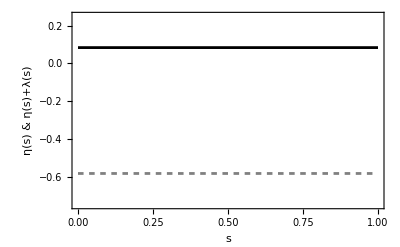

```mathematica
MSPlotEx2=Plot[{MMB[s,βL,γL,βH,γH],MSB[s,βL,γL,βH,γH]},{s,0,1},PlotStyle->{{GrayLevel[0],Thickness[0.005]},{GrayLevel[0.5],Thickness[0.005],Dashing[{0.01,0.01}]},{GrayLevel[0],Thickness[0.005],Dashing[{0.01,0.01}]}},Frame->True,FrameLabel->{StyleForm["s",FontSize->12],StyleForm["η(s) & η(s)+λ(s)",FontSize->12],StyleForm["Panel B.2",FontSize->12],""},PlotRange->{{0,1},{-0.75,0.25}}]
```

```mathematica
Export["c:\Documents and Settings\\bsg1\\My Documents\\BSG_WORK_19W4th\\Research\\HandbookOfSocialEcon_10Spring\Figure_SocPlan1.eps",GraphicsGrid[{{mHmLPlotEx1,mHmLPlotEx2}, 
 {MSPlotEx1,MSPlotEx2},{SocPlanPlotEx1,SocPlanPlotEx2}},Frame->All,ImageSize->1000]]
```

c:\Documents and Settings\bsg1\My Documents\BSG_WORK_19W4th\Research\HandbookOfSocialEcon_10Spring\Figure_SocPlan1.eps

### Example 3: Complicated Example # 1

```mathematica
αH=0.25;
βH=1;
γH=3/4;
```

```mathematica
αL=0;
βL=1/8;
γL=-3/4;
```

```mathematica
pH=0.3
```

0.3

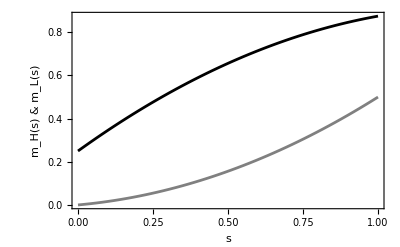

```mathematica
mHmLPlotEx3=Plot[{mH[s,αH,βH,γH],mL[s,αL,βL,γL]},{s,0,1},PlotStyle->{{GrayLevel[0],Thickness[0.005]},{GrayLevel[0.5],Thickness[0.005]}},Frame->True,FrameLabel->{StyleForm["s",FontSize->12],StyleForm["m_H(s)  &  m_L(s)",FontSize->12],StyleForm["Panel A.1",FontSize->12],""}]
```

```mathematica
mlist=Table[{s,m[s,αL,βL,γL,αH,βH,γH]},{s,0,1,0.01}];
t=Table[{s,m[0,αL,βL,γL,αH,βH,γH]},{s,0,1,0.01}];
u=Table[{1,m[0,αL,βL,γL,αH,βH,γH]+(m[s,αL,βL,γL,αH,βH,γH]-m[0,αL,βL,γL,αH,βH,γH])*s},{s,0,1,0.01}];
v=Drop[Sort[ConvexHull[Join[mlist,t,u]]],-199];
ConvHullm=mlist[[v]];
```

ConvexHull::duplicated: 3 duplicated point(s) ignored.

```mathematica
sL=mlist[[v[[1]]]]
sR=mlist[[v[[2]]]]
```

{0.,0.}

{0.83,0.743535}

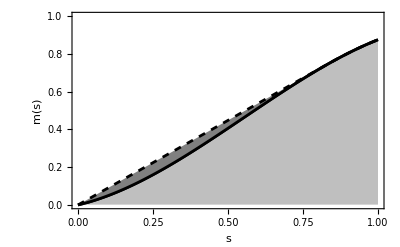

```mathematica
FilledListPlot[mlist,ConvHullm,t,Frame->True,FrameLabel->{StyleForm["s",FontSize->12],StyleForm["m(s)",FontSize->12],StyleForm["Panel C.1",FontSize->12],""},PlotJoined -> {True,True},PlotRange->{{0,1},{0,1}},SymbolShape->{None,None},PlotStyle->{{GrayLevel[0],Thickness[0.005]},{Dashing[{0.0125,0.0125}],GrayLevel[0],Thickness[0.005]},{GrayLevel[1],Thickness[0.001]}},Fills->{{{1,3},GrayLevel[0.75]},{{1,2},GrayLevel[0.5]}}]
```

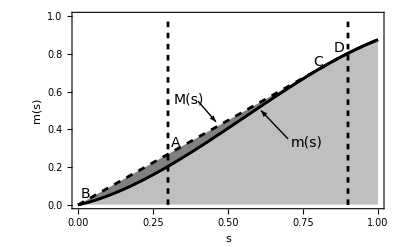

```mathematica
SocPlanPlotEx3=Show[%,Graphics[{{Thickness[0.005],GrayLevel[0],Dashing[{0.01,0.01}],Line[{{pH,0},{pH,1}}]},{Thickness[0.005],GrayLevel[0],Dashing[{0.01,0.01}],Line[{{pH+0.6,0},{pH+0.6,1}}]},
		Text[StyleForm["A",FontSize->14],{pH+0.01,0.33},{-1,0}],Text[StyleForm["B",FontSize->14],sL+{0.01,0.06},{-1,0}],Text[StyleForm["C",FontSize->14],sR-{0.015,-0.015},{1,0}],Text[StyleForm["D",FontSize->14],{pH+0.59,0.83},{1,0}],Arrow[{{0.40,0.55},{0.46,0.44}}],	Text[StyleForm["M(s)",FontSize->14],{0.32,0.56},{-1,0}],Arrow[{{0.70,0.35},{0.61,0.5}}],	Text[StyleForm["m(s)",FontSize->14],{0.71,0.33},{-1,0}]}]]
```

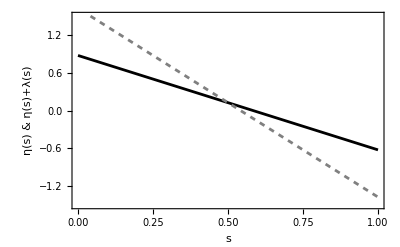

```mathematica
MSPlotEx3=Plot[{MMB[s,βL,γL,βH,γH],MSB[s,βL,γL,βH,γH]},{s,0,1},PlotStyle->{{GrayLevel[0],Thickness[0.005]},{GrayLevel[0.5],Thickness[0.005],Dashing[{0.01,0.01}]},{GrayLevel[0],Thickness[0.005],Dashing[{0.01,0.01}]}},Frame->True,FrameLabel->{StyleForm["s",FontSize->12],StyleForm["η(s) & η(s)+λ(s)",FontSize->12],StyleForm["Panel B.1",FontSize->12],""},PlotRange->{{0,1},{-1.5,1.5}}]
```

### Example 4: Complicated Example # 2

```mathematica
αH=0.25;
βH=1/8;
γH=-3/4;
```

```mathematica
αL=0;
βL=1;
γL=1;
```

```mathematica
pH=0.8
```

0.8

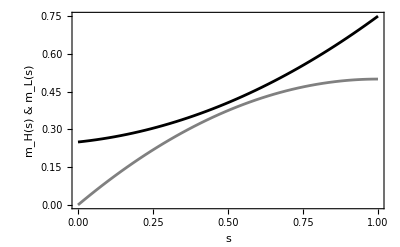

```mathematica
mHmLPlotEx4=Plot[{mH[s,αH,βH,γH],mL[s,αL,βL,γL]},{s,0,1},PlotStyle->{{GrayLevel[0],Thickness[0.005]},{GrayLevel[0.5],Thickness[0.005]}},Frame->True,FrameLabel->{StyleForm["s",FontSize->12],StyleForm["m_H(s)  &  m_L(s)",FontSize->12],StyleForm["Panel A.2",FontSize->12],""}]
```

```mathematica
mlist=Table[{s,m[s,αL,βL,γL,αH,βH,γH]},{s,0,1,0.01}];
t=Table[{s,m[0,αL,βL,γL,αH,βH,γH]},{s,0,1,0.01}];
u=Table[{1,m[0,αL,βL,γL,αH,βH,γH]+(m[s,αL,βL,γL,αH,βH,γH]-m[0,αL,βL,γL,αH,βH,γH])*s},{s,0,1,0.01}];
v=Drop[Sort[ConvexHull[Join[mlist,t,u]]],-199];
ConvHullm=mlist[[v]]
```

ConvexHull::duplicated: 3 duplicated point(s) ignored.

{{0.,0.},{0.01,0.0123634},{0.02,0.024457},{0.03,0.0362861},{0.04,0.047856},{0.05,0.0591719},{0.06,0.070239},{0.07,0.0810626},{0.08,0.091648},{0.09,0.102},{0.1,0.112125},{0.11,0.122027},{0.12,0.131712},{0.13,0.141185},{0.14,0.150451},{0.15,0.159516},{0.16,0.168384},{0.17,0.177061},{0.18,0.185553},{0.19,0.193864},{0.2,0.202},{0.21,0.209966},{0.22,0.217767},{0.23,0.225409},{0.24,0.232896},{0.25,0.240234},{0.26,0.247429},{0.27,0.254485},{0.28,0.261408},{0.29,0.268203},{1.,0.75}}

```mathematica
sL=mlist[[v[[30]]]]
sR=mlist[[v[[31]]]]
```

{0.29,0.268203}

{1.,0.75}

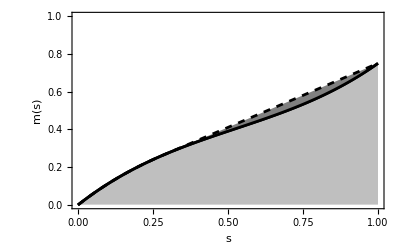

```mathematica
FilledListPlot[mlist,ConvHullm,t,Frame->True,FrameLabel->{StyleForm["s",FontSize->12],StyleForm["m(s)",FontSize->12],StyleForm["Panel C.2",FontSize->12],""},PlotJoined -> {True,True},PlotRange->{{0,1},{0,1}},SymbolShape->{None,None},PlotStyle->{{GrayLevel[0],Thickness[0.005]},{Dashing[{0.0125,0.0125}],GrayLevel[0],Thickness[0.005]},{GrayLevel[1],Thickness[0.001]}},Fills->{{{1,3},GrayLevel[0.75]},{{1,2},GrayLevel[0.5]}}]
```

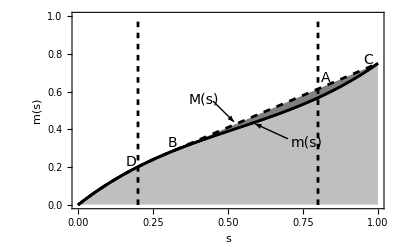

```mathematica
SocPlanPlotEx4=Show[%,Graphics[{{Thickness[0.005],GrayLevel[0],Dashing[{0.01,0.01}],Line[{{pH,0},{pH,1}}]},{Thickness[0.005],GrayLevel[0],Dashing[{0.01,0.01}],Line[{{pH+0.6,0},{pH+0.6,1}}]},{Thickness[0.005],GrayLevel[0],Dashing[{0.01,0.01}],Line[{{pH-0.6,0},{pH-0.6,1}}]},
		Text[StyleForm["A",FontSize->14],{pH+0.01,0.67},{-1,0}],Text[StyleForm["B",FontSize->14],sL+{0.01,0.06},{-1,0}],Text[StyleForm["C",FontSize->14],sR-{0.015,-0.015},{1,0}],Text[StyleForm["D",FontSize->14],{pH-0.605,0.23},{1,0}],Arrow[{{0.45,0.55},{0.52,0.44}}],	Text[StyleForm["M(s)",FontSize->14],{0.37,0.56},{-1,0}],Arrow[{{0.70,0.35},{0.59,0.43}}],	Text[StyleForm["m(s)",FontSize->14],{0.71,0.33},{-1,0}]}]]
```

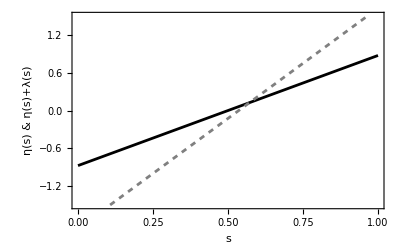

```mathematica
MSPlotEx4=Plot[{MMB[s,βL,γL,βH,γH],MSB[s,βL,γL,βH,γH]},{s,0,1},PlotStyle->{{GrayLevel[0],Thickness[0.005]},{GrayLevel[0.5],Thickness[0.005],Dashing[{0.01,0.01}]},{GrayLevel[0],Thickness[0.005],Dashing[{0.01,0.01}]}},Frame->True,FrameLabel->{StyleForm["s",FontSize->12],StyleForm["η(s) & η(s)+λ(s)",FontSize->12],StyleForm["Panel B.2",FontSize->12],""},PlotRange->{{0,1},{-1.5,1.5}}]
```

```mathematica
Export["c:\Documents and Settings\\bsg1\\My Documents\\BSG_WORK_19W4th\\Research\\HandbookOfSocialEcon_10Spring\Figure_SocPlan2.eps",GraphicsGrid[{{mHmLPlotEx3,mHmLPlotEx4}, 
 {MSPlotEx3,MSPlotEx4},{SocPlanPlotEx3,SocPlanPlotEx4}},Frame->All,ImageSize->1000]]
```

c:\Documents and Settings\bsg1\My Documents\BSG_WORK_19W4th\Research\HandbookOfSocialEcon_10Spring\Figure_SocPlan2.eps